## Inference from the data

I use the numbering for the initial 8 pools, which correspond to YP4, YP20, YP2, YP1, MP2, MP4, MP20, MP11.

#### Patterns of F_st, π_b, π_w

We observe sharp peaks in F_st that coincide with the mapped ROS and EL loci (Fig. x, Sx1). These are amongst the highest peaks genome-wide, and give strong evidence for selection at these loci. There is also an intermediate peak, left of EL, and a narrow dip at the centre of the ROS1 peak. These sharp features are superimposed on a broad increase in F_st across the ROS/EL region, spanning ~ 440kb. Table Sx gives estimates for pairwise diversity and divergence in regions defined to correspond to these features. In the following, we lay out scenarios that are consistent with the patterns of pairwise diversity and divergence, and estimate the associated parameters, including the time since a strong barrier to gene flow was established, and the rate of migration outside this barrier. We use simulations to find the uncertainty in these two parameters, and to show that the sharp peaks are significant, relative to the null model of neutral divergence, with and without gene flow.

Figure Sx1. Plot of F_st across the 930kb ROS/EL scaffold (top), and in the 220kb region immediately surrounding the ROS/EL region (bottom). Shading indicates the regions used to make parameter estimates. Grey: flanking regions, outside the influence of ROS/EL; pink: peaks in F_st at ROS1, intermediate, and at EL; blue: regions in-between ROS and EL. This may be covered by a figure in the main text, but it might be useful to show the regions used to define the windows. One could show multiple lines for different pairs of pools, but that gets crowded.  I suggest using values from just {4,5} for the actual inference.

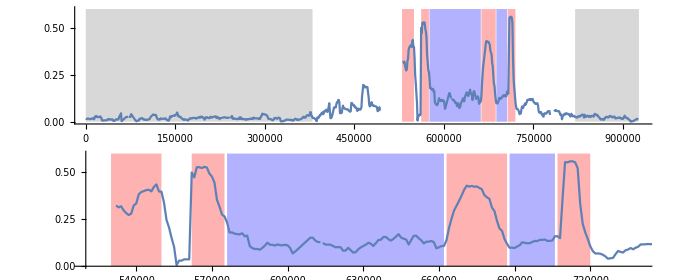

This version shows the three pairs of pools (black {4,5}, blue {3,6}, purple {1,8}) and shades some additional features - probably not needed

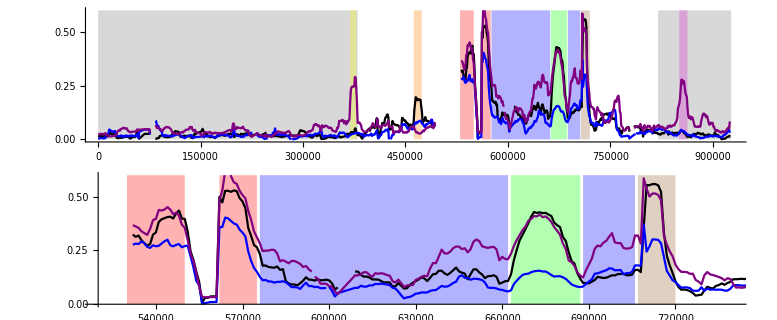

Table Sx1: Statistics for pools 4, 5, for  the regions defined in Fig. Sx, based on overlapping 10kb windows, spaced at 1kb intervals. Windows are included if their left edge is within the boundaries of the region (col. 2). π_1, π_2 give the pairwise diversity within pools 4, 5 (striatum and pseudomajus), and π_b the pairwise divergence between them.  The last two columns show the mean and maximum F_st.  Values of π are weighted by the number of informative sites in each window, defined as having coverage between 15 and 500. The mean F_st is calculated from these weighted averages of π.

region | boundaries | kb | # windows | # sites | π_1 | π_2 | π_b | mean F_st | max F_st
left of ROS | 0
380 | 380 | 360 | 1636278 | 0.0109429 | 0.0104005 | 0.011066 | 0.0181389 | 0.0509219
right of EL | 820
927 | 107 | 106 | 643667 | 0.00909371 | 0.00952096 | 0.00973102 | 0.0222543 | 0.0420804
left of ROS
right of EL | 0 | 380
820 | 927 | 487 | 466 | 2279945 | 0.0104208 | 0.0101522 | 0.0106891 | 0.0191934 | 0.0509219
between Ros/EL A
between Ros/EL B | 576 | 662
688 | 706 | 104 | 101 | 420244 | 0.00881096 | 0.00963057 | 0.0118643 | 0.125374 | 0.233314
ROS1 A
ROS1 B | 530 | 550
562 | 575 | 33 | 33 | 108623 | 0.00254687 | 0.00652744 | 0.0103648 | 0.391064 | 0.529218
ROS1 dip | 556
561 | 5 | 6 | 7008 | 0.00102895 | 0.00141002 | 0.00128973 | 0.0279949 | 0.0366392
third peak | 663
687 | 24 | 25 | 183534 | 0.0107394 | 0.00641349 | 0.0174623 | 0.341256 | 0.428983
EL | 707
720 | 13 | 14 | 34500 | 0.00815102 | 0.0105506 | 0.0153515 | 0.242918 | 0.558616

First, consider the sharp peaks at ROS and EL.  As argued in the main text, these are due to reduced diversity, rather than increased divergence. This can be seen in Fig. Sx2, which shows π_b, and π_w on either side, across the region. Peaks in F_st at ROS and EL (red, brown shading) appear to be due to reductions in diversity on both sides, whereas the intermediate peak (green shading) appears to be due to increased divergence. There are also regions where there is reduced diversity on one side, but where π_w is close to π_b on the other side (e.g. right of ROS, left of the intermediate peak, and left of EL); such an asymmetric loss of diversity does not increase F_st enough to give an obvious peak.  The relative roles of decreased diversity vs. increased divergence can be seen more clearly in Fig. Sx3, which plots mean π_w against π_b.  Away from the ROS/EL region, there is a wide scatter in π_w and π_b; these are closely correlated, reflecting low F_st (black dots). Between ROS and EL, there is a general increase in F_st (blue dots).   For all three pairs of pools, the F_st peaks at ROS and EL show lower diversity relative to this general distribution (large red, brown dots, below), whereas the intermediate peak shows higher divergence  (large green dot to the right).

Fig. Sx2. Plots of diversity within striatum and pseudomajus (black, blue resp.), and divergence between them (red), for three pairs of pools. Top: the whole 930kb region; bottom: the 220kb region between ROS and EL. Shading indicates regions, as in Fig. Sx1.

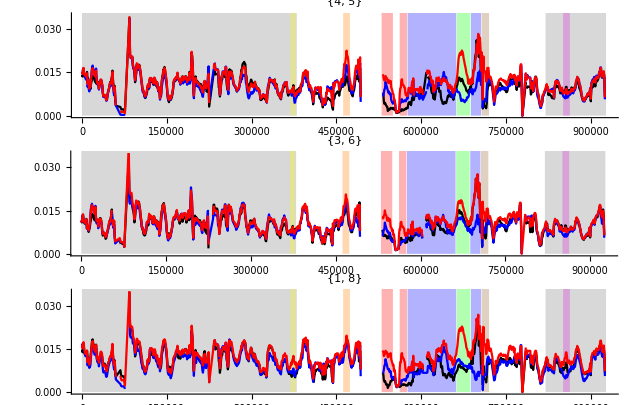

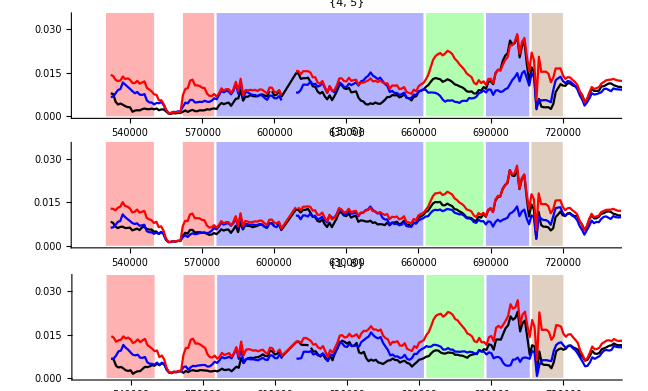

Figure Sx3. Pairwise divergence and diversity (π_b, π_w) are plotted for overlapping 10kb windows, for three pairs of pools. Small dots show flanking regions, away from the influence of ROS and EL (black) and between ROS and EL, excluding the intermediate peak (blue). Slightly larger dots show regions associated with sharp features: ROS1 (red), the dip within ROS1 (cyan), the intermediate peak (green) and EL (brown).  Grey lines show F_st=0, 0.1, …, 0.5, increasing downwards; large dots show the maximum F_st for each feature (Table Sx1). We may not want to include all these features.

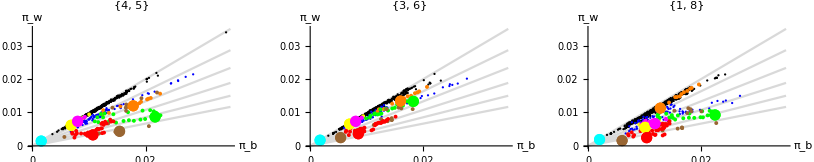

#### Explaining peaks at ROS and EL

The most obvious explanation for the two regions of reduced diversity at ROS and EL is that they are due to the sweep to fixation of one or more favourable mutations. Each such selective sweep would reduce diversity over a map distance r~2/τ, where τ is the time from origin of the mutation to its fixation. Indeed, sequences of four individuals from each side of the flower colour cline show fixation of distinct haplotypes at both Rosea and Eluta, as expected.(If we keep this sentence, need to include a figure of individual sequences, sent previously).  More precisely, the sweep of a single strongly selected mutation from low frequency to fixation eliminates diversity in an exponentially distributed region, of length 1/τ, on either side, totalling 2/τ on average (Barton, 1998).

```mathematica
{FindRoot[(1+a) ⅇ^-a ==0.025,{a,5}],FindRoot[1-(1+a) ⅇ^-a ==0.025,{a,0.1}]}
```

{{a→5.57164},{a→0.242209}}

Diversity is reduced over ~45kb and ~12kb at ROS and EL. If the causal loci are placed at the centres of each peak, they are ~160kb apart, corresponding to a recombination rate of 0.5cM, or 3.125 cM per Mb.  Hence, the reduction in diversity is over r~0.140, 0.038 cM,  respectively. This implies sweeps that had duration τ~1400, 5300 generations, respectively.  In a well-mixed population, τ~1/slog(4 N_e s), which would imply weak selection, s<0.001. However, spread across a spatially extended population takes much longer: an allele would take τ~(R/σ)/√(2s) generations to spread over a radius R, if genes diffuse at rate σ^2 per generation. Thus, narrow regions of reduced diversity are not inconsistent with strong selection - for example, a mutation with advantage s=0.2 would take ~1600 generations to spread over 1000 dispersal ranges. In any case, these estimates are very rough: the 95% confidence intervals for the sum of two exponential distributions, each with mean 1/τ, range from 0.24/τ to 5.57/τ, and in any case, there may have been multiple partial or soft sweeps.

Immediately after a ‘hard’ sweep, all diversity is eliminated close to the selected site. In fact, the average diversity has a minimum at π_w~0.0025 at ROS, and 0.0027 at EL (Table Sx1). After T generations, we expect that mutation at rate μ will generate π_w=2μT.  Assuming that μ=1.5×10^-8 per site per generation (Yang et al., 2015), this implies that very roughly, the most recent sweep occurred at T~83000 generations at ROS, and T~90000 at EL - or more recently if soft sweeps did not eliminate all diversity.

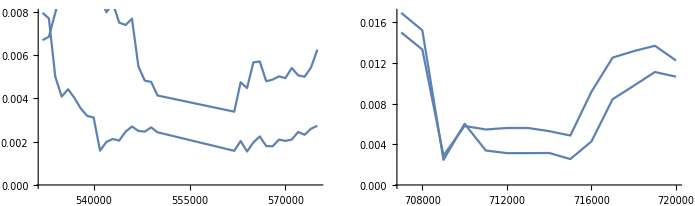

{0.00248066,0.00267451}

```mathematica
Show[GraphicsRow[Show[ListLinePlot[st[{4,5}][#]⟦All,{1,2}⟧],ListLinePlot[st[{4,5}][#]⟦All,{1,3}⟧]]&/@{{"ROS1 A","ROS1 B"},"EL"}]]
Min[st[{4,5}][#]⟦All,{2,3}⟧.{1/2,1/2}]&/@{{"ROS1 A","ROS1 B"},"EL"}
```

Diversity is reduced in both populations, at both loci, implying at least four, and possibly more, sweeps.  Flower colour is likely to be under strong stabilising selection, towards the phenotype that is locally most attractive to pollinators, and multiple substitutions may have occurred during the optimisation of a new phenotype.  For example, suppose that a ROS allele that caused restriction of magenta pigment somehow became established locally.  One can easily see how further mutations, possibly of smaller effect, that increase the attractiveness of the new phenotype could arise and spread within the new population. Such substitutions could occur at ROS, EL and at other loci that affect flower colour and pattern, and would be restricted in geographic range by their interaction with the first mutation.  However, this does not explain why diversity should be reduced within the original magenta population. Flower colour loci may experience recurrent selective sweeps, if for whatever reason the optimal phenotype changes sporadically.

#### The effects of a strong barrier to gene flow

Peaks in F_st are most often interpreted as being due to a local barrier to gene flow.  Could such a barrier somehow lead to reduced diversity, as we see here?  In principle, two divergent populations, each with low diversity, might meet, and mix. Across most of the genome, divergence would be eroded, and diversity would increase through mixing.  However, around local barriers, diversity would remain low, and divergence high, causing a peak in F_st.  Such a scenario is unlikely, for several reasons.  First, there is little indication of increased π_b at the two peaks.  Second, if diversity were generated by mixing, there would be a strong distortion of the allele frequency spectrum, with positive Tajima’s D, which is not observed [check - did Hugo calculate this?].  Third, the high F_st at the presumed barrier would be the relic of a high original divergence, which we do not see across the genus as a whole [check π_b across subspecies & species]

A further argument against a role for gene flow in shaping the two outermost peaks is peculiar to the ROS/EL example, which involves selection at two linked loci. This generates a strong barrier to gene flow throughout the intervening region, because two recombination events are required to transfer a neutral allele onto the opposite genetic background (see SIx). Thus, it is not possible to generate two separate and sharp peaks in F_st, as observed. If there is a strong barrier throughout the intervening region, then we expect sharp clines within this region.  This is indeed observed: whenever allele frequencies differ enough that a model can be fitted, a narrow cline is estimated, almost as narrow as for the phenotypic cline, and for the steep clines at SNP closest to ROS and EL. (Figure x).  Note that most SNPs within this region are polymorphic on either side, and so cannot show clines; this simply reflects the low divergence, and extensive shared polymorphism between the two populations.

The pattern of modest divergence and shared polymorphism in-between ROS and EL presumably reflects the relatively recent origin of selected differences at these loci, and hence of the barrier to gene flow.  We can make a rough estimate of the age of the barrier and of the rate of gene flow across the bulk of the genome, by comparing the mean genome-wide F_st~0.019 with the mean F_st~0.125 between ROS and EL (not including the three peaks; Table Sx1). We will be concerned with very long timescales, of order N_e, and so ignore spatial structure: in two dimensions, lineages are expected to diffuse widely, and in any case, over long timescales drastic changes in range make diffusion an inappropriate model.  Therefore, we simply assume that a single ancestral population split into two at time T in the past; each of these two has the same size, N_e, and the ancestral population is assumed to have been of size θ N_e. The diverging populations exchange N_e m individuals per generation.   SIx gives formulae for F_st as a function of T, M  and θ. Assuming that M=0 between ROS and EL (as implied by selection on two tightly linked loci; SIx), F_st would initially increase linearly with time, independent of θ, as F_st~t/(4 N_e); thus, the observed F_st~ 0.125 would build up in t=0.5 N_e generations; the exact solution, with relative size of the ancestral population θ=2, is 0.54 N_e. Outside the barrier, F_st quickly reaches an equilibrium between gene flow and drift, such that  F_st= 1/(1+16 N_e m); the observed F_st~ 0.019 is consistent with exchange of N_e m=3.2 individuals per generation. (This should be regarded as an “effective number”, since the actual relation depends on the detailed population structure).   We can estimate N_e from the diversity outside the ROS/EL region,  π_w~0.010 (Table Sx1), which is expected to equal 8 N_e μ for a well-mixed ancestral population of θ N_e diploid individuals, with θ=2. (Since N_e m is large, diversity is hardly affected by the population split) Assuming μ=1.5×10^-8 as before, N_e~8.3×10^4, and so T~0.54 N_e~45000 generations.  This is of the same order as the estimated time since the selective sweeps, 83-90000 generations, which were made independently, from the residual diversity below the twin peaks. However, the data are also consistent with secondary contact between divergent populations, with F_st<0.12, at some time correspondingly more recent than 45000 generations: because F_st outside the ROS/EL region equilibrates quickly, these scenarios cannot be distinguished (Fig. x).

Note that we can pick out the effects of a strong barrier to gene flow on cline width and in slightly elevating F_st only because the barrier extends over 0.5cM and >200kb, between two closely linked loci.  Single selected loci would generate a barrier over a narrow region, which would be hard to detect unless it occurred in a region of low recombination.  In addition, we have independent evidence from genetic mapping and narrow clines that there are in fact two selected loci, at ROS and at EL.

#### Testing the significance of the F_st peaks

We know that there is currently a strong barrier to gene flow across the ROS/EL region, and that over time, this will lead to a broad island of increased F_st.  This increase is due both to accumulating divergence (or, prevention of erosion of divergence after secondary contact), and to a decrease in diversity as one large population is split into two smaller ones by the barrier. We now ask whether the sharp peaks at ROS and EL, and the various other fluctuations across this region, are significant, relative to a null model in which a barrier formed at some time T in the past, and divergence accumulated since that split. Under the null model, fluctuations are due to sampling a limited number of individuals from the population; random variation in SNP frequencies; and variation in the ancestry of different blocks of genome. We will see that variation in F_st is largely due to variation in ancestry, rather than being limited by sample size or by the number of SNP.

The distribution of π_w, π_b simulated under a simple model of a split between two well-mixed populations is substantially narrower than the wide range observed.  The most obvious explanation for this is that the Antirrhinum majus population is structured, both in space and time, which greatly inflates the variation in ancestry along the genome (Charlesworth et al., 2003); variation in mutation rate and recombination rate along the genome may also cause variation in π_w.  We therefore simulate only from the time of the split, and use an initial pattern of SNP that is drawn from the 380kb flanking regions, left and far from Ros/EL (Table Sx1).  Thus, we start with a pattern of SNP frequencies that is typical of the Antirrhinum majus genome, and do not make any assumptions about its deep history. Rather than simulating discrete loci, we track the origins of each simulated genome, assigning blocks to one or other of the ancestral genomes. This allows us to separate variation in ancestry from variation due to the random choice of SNP. We simplify by comparing a complete barrier with gene flow N_e m=3.2, rather than modelling selected loci at ROS and EL explicitly: it is not clear how to do this, since selection would scale to unreasonably high values.  Thus, we do not model the variation in divergence due to changes in barrier strength along the genome.  However, in SIx, we do calculate the expected coalescence times along the genome.

It is not feasible to directly simulate structured populations with N_e~83000, over times of the same order.  Therefore, we follow Hill and Robertson (1966) by scaling the simulations, running smaller populations for a shorter time. We simulate two populations, each with N_e=100 diploid individuals, for up to 100 generations. The populations either exchange genes at a rate N_e m=3.2, or evolve separately.  There are 5 crossovers per generation, which corresponds to a recombination rate in Antirrhinum of 5*100/83000 = 0.0060, equivalent to 193kb, or approximately 19×10kb windows.  The simulated mutation rate is 2.7 mutations per genome, which corresponds to μ=2.7×100/(83000 193000)=1.7*10^-8 per site per generation. SNP frequencies are analysed exactly as for the real data, with the number of SNP being drawn from random 10kb windows, taken from the 380kb flanking region.

Fig. Sx4  Mean diversity within populations, π_w, plotted against divergence, π_b, for simulations, at T=0.4 N_e generations.  The left plot shows results from 4 simulations: two replicates with N_e m=3.2 (blue/purple) and two with no gene flow (black/grey). For each simulation, the genome is assigned to 19 windows, each representing 10kb.  The right plot shows the same four replicates, but each with 100 random draws of the SNP from the reference regions.  The large dots show the three F_st peaks, at ROS, EL and in-between (red, brown, green), as in Fig. Sx3 (These need to be superimposed).

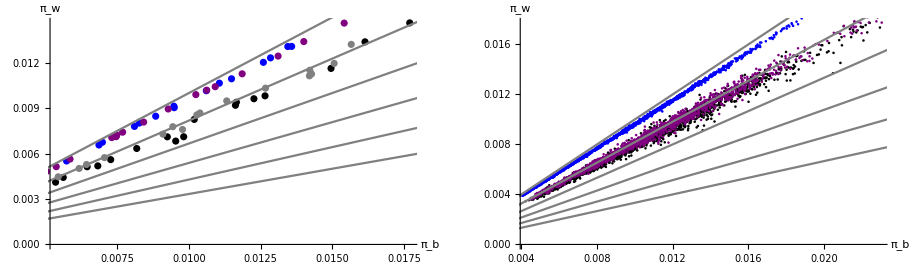

The joint distribution of π_w, π_b in simulations is similar to that in the data (compare Figs. Sx3, Sx4), and the F_st peaks lie well outside the distribution with a complete barrier.  SInce variation in π_w,π_b is strongly correlated, and since the wide variation in π_w, π_b is taken as given from the data, we now focus on the distribution of F_st.  WIth gene flow, this quickly reaches an equilibrium (Fig. Sx, right), at the predicted value.  With no gene flow (Fig. Sx, left), F_st increases; the best fit to the observed F_st = 0.12 is t=0.45 N_e, with confidence interval xx, based on the substantial variation between replicates.

Fig. Sx5  Increase in F_st over time for 10 replicate simulations, with N_e m=0 or 3.2 (left, right); each line is the average of 100 replicate draws of the SNP.  The blue dotted line shows the observed F_st=0.019 outside ROS/EL, and the black dotted line F_st=0.12 in-between ROS and EL.  Red lines show the theoretical prediction, based on expected coalescence times (SIx).  The upper orange line at right shows the expected decrease, starting from F_st=0.1, showing how quickly divergence is eroded following secondary contact.  Omit the middle panel, and update - Fst is too high on the RHS.

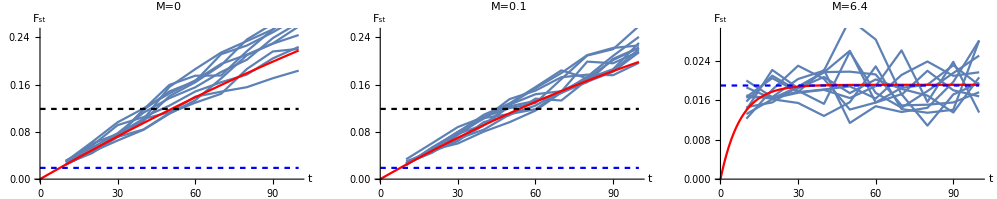

We next examine the distribution of F_st, in order to find whether the various peaks are significant, relative to the null model of divergence across a strong barrier.  Figure Sx6 shows that with the density of SNP in the actual data (57167 in 930Mb), variation in F_st is about equally due to random variation in SNP frequency, and to variation in the underlying ancestry. Testing the significance of peaks in F_st is not straightforward, because these consist of a set of correlated values from adjacent windows; therefore, we compare statistics gathered from simulations in the same way as they were calculated from the actual data. We ask, how likely it is that the maximum F_st across the region would be as large, or larger, than the observed? Assuming a normal distribution, which fits well, the peaks at ROS, at EL, and in-between (maximum F_st=0.529, 0.559, 0.429 respectively) correspond to z=xx - all of which are highly significant.  No correction for multiple testing is needed, because these peaks are at or between known causal loci, and because we are simulating the maximum F_st seen across this whole region.  In the absence of that knowledge, these peaks would not be significant, at least taken one by one (check)

Fig. Sx6. The distribution of F_st with gene flow (N_e m=3.2; left) and without (right), for 10 replicate simulations, at t=0.4 N_e. Each distribution represents variation in F_st due to 100 random draws of the SNP, conditional on the ancestry.  For N_e m=3.2, the standard deviation between replicates, due to random ancestry, is xx, and within replicates, due to random SNP, is xx; for N_e m=0, the s.d. are ?? respectively.

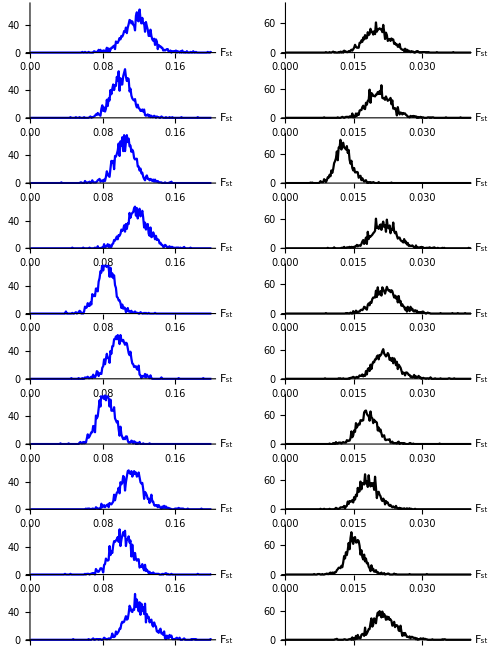

Look at the significance of the asymmetric loss of diversity; cite Schlotterer for this.

#### Interpreting fluctuations in F_st

As well as the striking peaks in F_st at ROS and EL, there are other sharp features across this region: an intermediate F_st peak between ROS and EL (green shading on Fig. Sx2); a ~5kb region of reduced diversity and divergence in the middle of the ROS peak; regions in which diversity is lower on one side, but π_b~π_w on the other; and smaller features which may appear only in some comparisons (Fig. Sx1).  These could have a variety of causes. If a mutation sweeps across both hybridising populations, it would decrease diversity but not divergence (Cruickshank and Hahn, 2014), and give a dip in F_st. If a mutation sweeps through only one population, it will reduce diversity on only one side, giving a smaller F_st peak. If a block of genome introgresses from a divergent population or species, and sweeps to fixation within one of the two hybridising populations, it would generate an F_st peak with increased divergence, rather than reduced diversity.  Comparisons between different pairs of samples may give different patterns if divergence occurs at different places; in particular, we know that there is substantial divergence across the pass at the head of the Planoles valley (F_st = ?? between pools 1, 3). Once a strong barrier to gene flow is established, sweeps in that region (which may or may not be related to flower colour) will tend to be trapped, so that sharp features will accumulate there (Navarro and Barton, 2003).  It may be possible to distinguish these possibilities by sampling individual haplotypes from a broad range, but we do not speculate further here.  The aim of this section has been to show that such sharp features cannot be explained simply by a strong barrier to gene flow across the whole ROS/EL region - though sweeps may accumulate at such a barrier, leading to sharp F_st peaks. Our simulations show that these various peaks in F_st are significant, relative to the expected broad increase in F_st that is generated by such a barrier.

### References

Barton N. H., 1998 The effect of hitch-hiking on neutral genealogies. Genetical Research 72: 123–133.

Charlesworth B., Charlesworth D., Barton N. H., 2003 The effects of genetic and geographic structure on neutral variation. Annu. Rev. Ecol. Syst. 34: 99–125.

Hill W. G., Robertson A., 2009 The effect of linkage on limits to artificial selection. Genetical Research 8: 269–294.

Navarro, A. & Barton, N.H., 2003   Accumulating postzygotic isolation genes in parapatry: a new twist on chromosomal speciation. Evolution 57:447-459

Yang, S., Wang, L., Huang, J.,  Zhang, X, Yuan, Y, Chen, J-Q., Hurst, L. D., Tian, D. 2015. Parent-progeny sequencing indicates higher mutation rates in heterozygotes. Nature 523: 463-467

#### To do

Include mutations in the simulated data
Test significance of Fst and also (π_w1-π_w2)/(π_w1+π_w2) across windows. 
Discuss Yeaman et al., and earlier simulation schemes such as Balding & Beaumont